# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}]
$Path=Join[$Path,FileNames[packageDirectory]];
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\1DPackage\*

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedNewMethod"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseAEREAL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Aereal",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
reduce=2;
path1=FileNameJoin[{baseAEREAL,"Aereal1.png"}];
path2=FileNameJoin[{baseAEREAL,"Aereal2.png"}];
pathResult=FileNameJoin[{baseAEREAL,"AerealResult.png"}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];

reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];

iaa=reduire[ColorConvert[clean@Import[path1],"GrayScale"],reduce];
ibb=reduire[ColorConvert[clean@Import[path2],"GrayScale"],reduce];
iccolor=reduire[clean@Import[pathResult],reduce];

Show[iaa]
```

-Graphics-

## Image sections

```mathematica
(*{1,44},{1,102} arbitrary size to make the method faster *)
listDims={{500,500}}
ims=Table[
nx=dims[[1]]/reduce;
ny=dims[[2]]/reduce;


{ia,ib,icolor}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{iaa,ibb,iccolor};
{ia,ib}
,{dims,listDims}]
```

{{500,500}}

{{-Graphics-,-Graphics-}}

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## Little functions

```mathematica
bigTest[steps_,dis_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[
ic=move[im[[1]],dis];
depth=stereoDepth[n,u,listv0,condition,im[[1]],ic,minmax[[2]],minmax,Range[1,103,steps],Range[1,45],e,"ConstrainedNewMethod"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,45}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,45}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,45}];

(* We create g0 *)
g0=Graphics[{PointSize[0.009],Table[affiche[#,45-y]&/@realPVTable[[y]],{y,1,45}]}];
g0=Rasterize[Show[im[[1]],g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## Big Tests

### Test Design

For a synthetical displacement of 0.1:
 
•	Initial values range: {{0,1},{-1,1},{-1,0},{-2,2}}
•	Selection criteria:
	•	We filter direction (positive solutions only)
	•	Range {0, 1} 
	•	No errors allowed
•	Magnitude threshold for gradient is e=0.0001

(* Criterias to select a solution *)

newValCon=Select[tableNewVals,(#[[3]]==”converged”&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValAny=Select[tableNewVals,((#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&&#[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValOk=Select[tableNewVals,((#[[3]]==”ok”||#[[3]]==”oksign”||#[[3]]==”okmag”)&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
noFakeConverge=Select[tableNewVals,(#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&,1];

### Test Run

```mathematica
(* Test values *)
testLevels={{1,1}};
dis=0.1;
e=0.0001;
n=0;
u=0;
steps=1;
```

```mathematica
topbotValuesList={{0,0.5},{-0.5,0.5},{0,1},{-1,1},{0,2},{-2,2}};
```

```mathematica
(* Creating initial values *)
range={0,1};
r=Random[];
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
```

```mathematica
(* Scaling results *)
scale={ -2,2};
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
```

```mathematica
levelTable=Table[Table[

(* Creating condition *)
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbotValues[[1]]<Total[x[[1;;2]]]<topbotValues[[2]];


bigTest[steps,dis,n,u,listv0,condition,e,{levels},ims]

,{levels,testLevels}],{topbotValues,topbotValuesList}];
```

```mathematica
(*selectrion criteria, level, image, extra, kind of result, rows *)
Dimensions[levelTable]
```

{6,1,1,1,4}

### Histogram Grid 1

```mathematica
fontsize=20;
imagesize=500;
maxvalue={{-0.1,1.1},{0,800}};
bar=30;
```

```mathematica
histogramGrid=Table[
Table[

convergedData=Flatten[levelTable[[which,idxims,1,1,1,All,All,2]]];
okData=Flatten[levelTable[[which,idxims,1,1,2,All,All,2]]];
nonConvergedData=Flatten[levelTable[[which,idxims,1,1,3,All,All,2]]];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=(Length[Flatten[DeleteDuplicates[#]&/@Round[levelTable[[which,idxims,1,1,1,All,All,1]]]]])/(103.*45.);
meanError=Mean[Abs[0.1-convergedData]];

Histogram[{convergedData, nonConvergedData,okData},bar,
PlotLabel->Column[{
Style[Row[{"Criteria range= ","[",Row[topbotValuesList[[which]],","],"]"}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Mean error= ",NumberForm[meanError,2]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Density= ",NumberForm[density,3]}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,
Alignment->Center],
PlotRange->maxvalue,
ImageSize->imagesize,
AxesLabel->{Style["v",FontSize->fontsize,FontFamily->"Times",Italic],Style["n",FontSize->fontsize,FontFamily->"Times",Italic]},ChartStyle->{LightOrange,LightBlue,LightGreen}]
,{which, Length[topbotValuesList]}],{idxims,Length[ims]}];
```

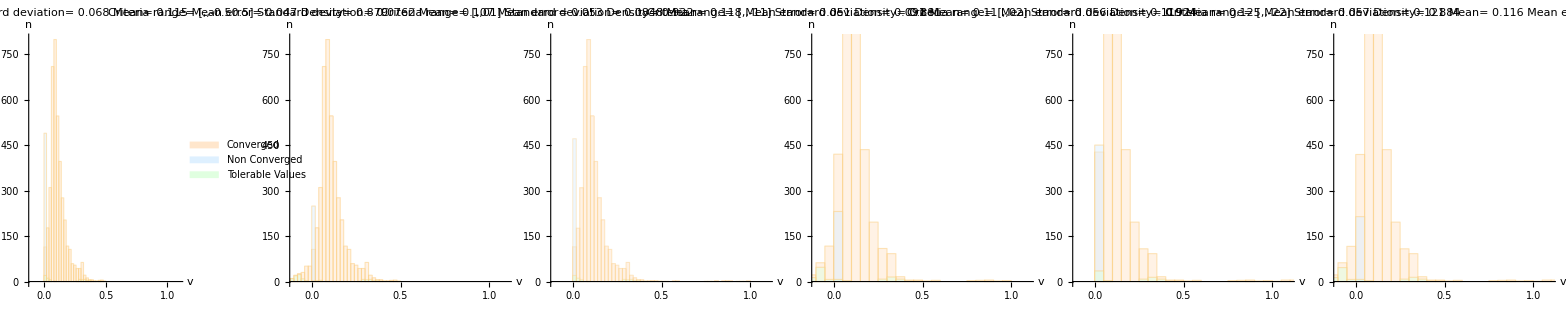

```mathematica
hFinal=Legended[
Grid[histogramGrid],
Placed[SwatchLegend[{LightOrange, LightBlue, LightGreen},{"Converged", "Non Converged", "Tolerable Values"},LegendLayout->"Row"],Below]]
```

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-hist.pdf"}],hFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\synaereal-criteria-hist.pdf

### Images

```mathematica
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
imagesTable=Table[

{levelTable[[which,1,1,1,4]],Style[Style[Row[{"Criteria range= ","[",Row[topbotValuesList[[which]],","],"]"}],FontSize->fontsize,FontFamily->"Times",Italic],FontSize->fontsize,FontFamily->"Times",Italic]}

,{which, Length[topbotValuesList]}];

imFinal=Legended[Grid[Flatten[imagesTable,{{2},{1}}]],legendBar]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Criteria range= [,,00.5] | Criteria range= [,,-0.50.5] | Criteria range= [,,01] | Criteria range= [,,-11] | Criteria range= [,,02] | Criteria range= [,,-22]

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],imFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\synaereal-criteria-im.pdf

### Table

```mathematica
tableValues=Table[
Table[

convergedData=Flatten[levelTable[[which,idxims,1,1,1,All,All,2]]];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=(Length[Flatten[DeleteDuplicates[#]&/@Round[levelTable[[which,idxims,1,1,1,All,All,1]]]]])/(103.*45.);
meanError=Mean[Abs[0.1-convergedData]];

{std,mu,density,meanError}

,{idxims,Length[ims]}],{which, Length[topbotValuesList]}];
```

```mathematica
makeTable=Table[
values=tableValues[[All,All,which]];
greenRedColor[z_]:=Blend[{Green,Red},Rescale[z,MinMax[values],{0,1}]];
greenRedColor2[z_]:=Blend[{Red,Green},Rescale[z,MinMax[values],{0,1}]];


TableForm@Map[Item[#,
Background->Directive[Opacity[0.7],If[which==3,greenRedColor2[#],greenRedColor[#]]]
]&,
values,
{2}]

,{which, Dimensions[tableValues][[3]]}];

t=Prepend[{makeTable},{"std","mu","density","muerror"}];
t2=MapThread[Prepend,{t,{"",Table[{Row[topbotValuesList[[i]],","]},{i,Length[topbotValuesList]}]//TableForm}}];
Grid[t2]
```

| std | mu | density | muerror
,,00.5
,,-0.50.5
,,01
,,-11
,,02
,,-22 | 0.0680197
0.07616
0.084758
0.091041
0.118775
0.120711 | 0.114797
0.106791
0.118363
0.110225
0.124698
0.116032 | 0.878533
0.921683
0.881122
0.924272
0.883711
0.926645 | 0.0474785
0.0525688
0.0508459
0.0557579
0.0569772
0.0612621

### More in depth

```mathematica
lvl=5;
```

```mathematica
k=42;
{ka,kb}=ImageData[#][[k]]&/@{ia,move[ia,dis]};
pyra=pyrFuncGen[ka,lvl];
pyrb=pyrFuncGen[kb,lvl];
pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];
```

```mathematica
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && 0<Total[x[[1;;2]]]<2;
```

```mathematica
lineTest[n,u,listv0,condition,Range[1,ImageDimensions[ia][[1]]],pyrab[[1;;1]],e,"ConstrainedNewMethod"]
```

{{0.00495689,0.00371929,converged,1},{0.0067059,0.000876034,converged,2},{0.0372386,0.0379422,converged,3},{0.0480769,0.0492095,converged,4},{0.0579585,0.0566328,converged,5},{0.0483641,0.0486495,converged,6},{0.0435544,0.0416798,converged,7},{0.0827012,0.108908,converged,8},{0.019642,0.0171329,converged,9},{0.0539709,0.0611335,converged,10},{0.,0.,sign,11},{0.0334006,0.0327997,converged,12},{0.0487997,0.0520477,converged,13},{0.142419,0.174613,converged,14},{0.0304238,0.0307784,converged,15},{0.0582812,0.0611344,converged,16},{0.0749606,0.0690248,converged,17},{0.0653088,0.0612965,converged,18},{0.0707723,0.0682849,converged,19},{0.0594874,0.055814,converged,20},{0.0671295,0.0685046,converged,21},{0.0852789,0.0733091,converged,22},{0.0433364,0.0388189,converged,23},{0.0624341,0.0750688,converged,24},{0.0100707,0.000329095,converged,25},{0.0370239,0.0376032,converged,26},{0.0443123,0.0454273,converged,27},{0.,0.,sign,28},{0.0396523,0.0435806,converged,29},{0.1592,0.157785,ok,30},{0.0312798,0.0302298,converged,31},{0.0626122,0.0707617,converged,32},{0.00275906,0.000642788,converged,33},{0.0502036,0.0578487,converged,34},{0.,0.,sign,35},{0.0361363,0.0380518,converged,36},{0.042518,0.0426006,converged,37},{0.0508438,0.0520808,converged,38},{0.0756046,0.0747278,converged,39},{0.082211,0.0705538,converged,40},{0.0648233,0.0608562,converged,41},{0.046583,0.0452928,converged,42},{0.0893887,0.186504,converged,43},{0.0248121,0.02536,converged,44},{0.043379,0.0449623,converged,45},{0.,0.,sign,46},{0.,0.,sign,47},{0.0290202,0.0304337,converged,48},{0.0414694,0.0415205,converged,49},{0.0513778,0.0528104,converged,50},{0.0794852,0.0788512,converged,51},{0.104252,0.0828455,converged,52},{0.065418,0.0611636,converged,53},{0.0556141,0.0546576,converged,54},{0.0709621,0.0683903,converged,55},{0.0527922,0.0493943,converged,56},{0.,0.,sign,57},{0.050147,0.0654345,converged,58},{0.13697,0.081926,converged,59},{0.0358043,0.0311527,converged,60},{0.0671139,0.0834174,converged,61},{0.00179008,0.00604653,converged,62},{0.0254578,0.0296492,converged,63},{0.0344511,0.0332788,converged,64},{0.050838,0.0560586,converged,65},{0.150194,0.146225,converged,66},{0.0280966,0.0321227,converged,67},{0.0706408,0.0721619,converged,68},{0.127455,0.10916,converged,69},{0.,0.,sign,70},{0.0370319,0.0343462,converged,71},{0.,0.,sign,72},{0.0308604,0.0299388,converged,73},{0.0673564,0.0786122,converged,74},{0.00262448,0.0133722,converged,75},{0.0369531,0.0369542,converged,76},{0.0752421,0.0815103,converged,77},{0.100143,0.0736647,converged,78},{0.0363624,0.0404897,converged,79},{0.0395031,0.0348972,converged,80},{0.0862175,0.15626,converged,81},{0.0239308,0.0244671,converged,82},{0.0441278,0.0456613,converged,83},{0.0744407,0.075719,converged,84},{0.0925606,0.0744634,converged,85},{0.0375472,0.0333095,converged,86},{0.075954,0.0935794,converged,87},{0.,0.,mag,88},{0.115297,0.13011,converged,89},{0.032697,0.0226138,converged,90},{0.075891,0.133556,converged,91},{0.0216182,0.0205278,converged,92},{0.0624658,0.0707115,converged,93},{0.,0.,sign,94},{0.0342632,0.0301609,converged,95},{0.0668847,0.0737078,converged,96},{0.0627417,0.055304,converged,97},{0.0629929,0.0789653,converged,98},{0.0204548,0.0185172,converged,99},{0.0370796,0.0372997,converged,100},{0.0562435,0.0589889,converged,101},{0.105323,0.113804,converged,102},{0.015573,0.0184381,converged,103}}

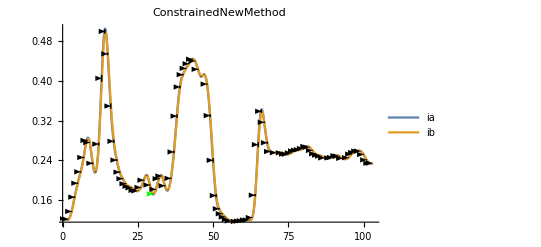

```mathematica
seeAllLine[n,u,listv0,condition,Range[1,103],pyrab[[1;;1]],e,"ConstrainedNewMethod"]
```